## Common elements

References:
[MSc] F.Hekhorn, “Sub-leading Terms in Heavy Quark Soft Gluon Resummation”, MSc Thesis Universität Tübingen, Germany, 2015.
[Bonc] R. Bonciani, S. Catani, M. L. Mangano, and P. Nason, “NLL resummation of the heavy quark hadroproduction cross-section,” Nucl.Phys. B529 (1998) 424–450, arXiv:hep-ph/9801375 [hep-ph].
[InvMelTh] https://en.wikipedia.org/wiki/Mellin_inversion_theorem
[MP] S. Catani, M. L. Mangano, P. Nason, and L. Trentadue, “The resummation of soft gluons in hadronic collisions,” Nuclear Physics B 478 no. 1–2, (1996) 273 – 310.

```mathematica
(* load packages *)
AppendTo[$Path, ToFileName[{$HomeDirectory,"Physik/PhD/MMa"}]];
Get["MellinTrafoLogCoeffs.m"]
Get["SudakovFactor.m"]
Get["NumericMellinTrafo.m"]
Needs["HEPMath`LHAPDF`"]
(*Get["PdfUtils.m"]*)
Get["zPlot.m"]
Needs["PlotLegends`"]
```

```mathematica
(* give concrete parameters *)
CFCASub = {CF -> 4/3, CA -> 3};
(* @param mQ override default mass *)
(* @param αμ override default running coupling from PDF *)
Options[toN] = {"channel" -> "γg","Q" -> "c","pdfParams"-> {"cteq66",0}, "mQ"-> -1, "αμ"-> -1};
toN[opts:OptionsPattern[]] := Module[{Q,ch,cαμ,r,l,p},
Q=OptionValue["Q"];
ch=OptionValue["channel"];
r=SudakovFactor`getRules[ch];
(* params related to quark *)
l = {
nl-> Switch[Q,"t",5,"b",4,"c",3,_,Throw["unknown quark"]] ,(* number light flaours *)
eQ-> Switch[Q,"t",2/3,"b",-1/3,"c",2/3,_,Throw["unknown quark"]] ,(* electric charge *)
mQ-> If[OptionValue["mQ"] >0,OptionValue["mQ"],Switch[Q,"t",173.070,"b",4.180,"c",1.5(*1.275*),_,Throw["unknown quark"]]], (* [GeV] *)
μ-> mQ (* [GeV] *)
};
(* params related to PDF *)
cαμ=OptionValue["αμ"];
p={αμ-> If[NumericQ[cαμ]&& cαμ≤ 0,
Evaluate@Module[{pdfId,α},
pdfId=LHAPDFOpen@@OptionValue["pdfParams"];
α=LHAPDFAlphaS[pdfId,μ//.l];
LHAPDFClose[pdfId];
α
],
cαμ]};
(* join all *)
Join[r,CFCASub,l,p,{lnRScale4->lnScale4,lnFScale4 ->lnScale4,lnScale4-> Log[μ^2/(4*mQ^2)]}]
];
nLandau =N[Exp[1/(2αμ*b0)]//.toN[]]
```

6.94572

```mathematica
(* transformations *)
ρ2β[ρ_]=Sqrt[1-ρ];
β2ρ[β_]=1-β^2;
ρ2η[ρ_]=1/ρ-1;
η2ρ[η_] = 1/(1+η);
β2χ[β_]=(1-β)/(1+β);
χ2β[χ_]=(1-χ)/(1+χ);
s2ρ[s_]=4*mQ/s;
vars2ρ[e_] :=e//. {β->ρ2β@ρ,η->ρ2η@ρ,χ->β2χ@ρ2β@ρ};
```

```mathematica
(* compute common resummation functions *)
Do[commonG[n] = getG[n],{n,1}]
```

```mathematica
(* build resummation factor *)
ΔLL = Exp[lnN * commonG[1][αμ*b0*lnN]];
```

```mathematica
(* used colors *)
Table[Graphics[{c,Disk[]},ImageSize-> 50],{c,ColorData[3,"ColorList"]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Born cross section

```mathematica
(* Born cross sections of unpol. photoproduction *)
Born = π/4 ρ(-(3-β^4)Log[χ]+2β^3-4β);
Module[{a,mlnχ},
a = {0.9991,−0.4828,0.2477,−0.0712};
mlnχ[u_,v_]=n↦Beta[n+u,v/2+1](PolyGamma[n+u+v/2+1]-PolyGamma[n+u])+2*Sum[a[[j]]*Beta[n+u,(v+j)/2+1],{j,Length@a}];
BornN = n↦Evaluate[π/4*(-4Beta[n+1,3/2]+2Beta[n+1,5/2]+3*mlnχ[1,0][n]-mlnχ[1,4][n])];
]
```

```mathematica
(* deduce series of Born in β *)
(*Series[-Log[β2χ@β],{β,0,11}]
Table[2(1/(2k-1)),{k,6}]
Series[-(3-β^4)Log[β2χ@β],{β,0,11}]
{6,2}~Join~Table[2(3/(2k-1)-1/(2k-5)),{k,3,6}]
{2,2,-4-4/5}~Join~Table[2(3/(2k-1)-3/(2k-3)-1/(2k-5)+1/(2k-7)),{k,4,8}]*)
BornβSerCoeff[1] =1;
BornβSerCoeff[2] =1;
BornβSerCoeff[3] =-12/5;
BornβSerCoeff[k_Integer] := (3/(2k-1)-3/(2k-3)-1/(2k-5)+1/(2k-7))/;k>3;
(* check *)
Series[2/π*(vars2ρ@Born/.{ρ-> β2ρ@β}),{β,0,21}]
Table[BornβSerCoeff@k,{k,11}]
(* the coefficients sum up to 0 *)
(* maybe this results hold more generally for all kind of partonic Born cross sections? at least it does for hadro-quark *)
BornβSerCoeff[1]+BornβSerCoeff[2]+BornβSerCoeff[3]+Sum[(3/(2k-1)-3/(2k-3)-1/(2k-5)+1/(2k-7)),{k,4,∞}]
(* numeric check *)
Table[N@Total[CoefficientList[Normal@Series[(Born//.{χ-> β2χ@β,ρ-> β2ρ@β}),{β,0,2*k-1}],β]],{k,{1,2,3,5,10,20,50,100,1000}}]
```

β+β^3-(12 β^5)/5+(52 β^7)/105+(4 β^9)/105-(4 β^11)/1155-(92 β^13)/9009-(68 β^15)/6435-(116 β^17)/12155-(524 β^19)/62985-(244 β^21)/33915+O[β]^22

{1,1,-12/5,52/105,4/105,-4/1155,-92/9009,-68/6435,-116/12155,-524/62985,-244/33915}

0

{1.5708,3.14159,-0.628319,0.20944,0.143301,0.0759506,0.0310652,0.015625,0.00157001}

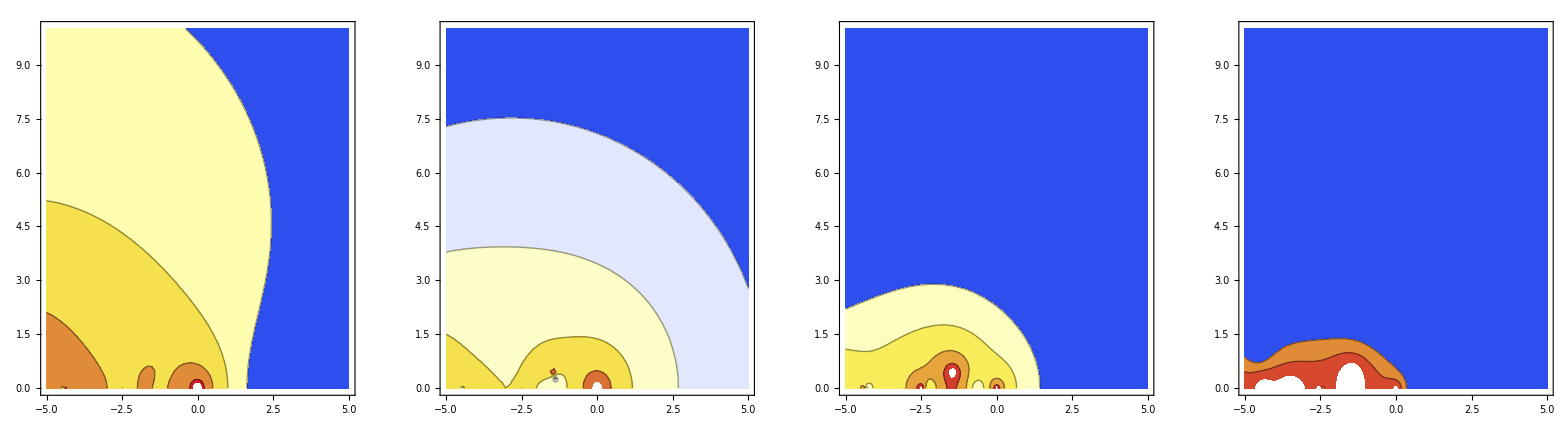

```mathematica
(* check convergence in N-space: *)
Module[{orders,BornMaxSer,BornSers,BornSerβList,BornSerNs,m},
orders = {1,3,5,9};
(* compute series *)
BornMaxSer=Normal@Series[(Born//.{χ-> β2χ@β,ρ-> β2ρ@β}),{β,0,Max@orders}];
BornSers = Table[Normal@Series[BornMaxSer,{β,0,v}],{v,orders}];
(* transform to N *)
BornSerβList=(s↦CoefficientList[s,β])/@BornSers;
BornSerNs=(l↦(n↦Evaluate[l//.{m-> n}]))/@((l↦Total[MapIndexed[Function[{c,ind},c*Beta[m,(First@ind-1)/2+1]],l]])/@BornSerβList);
GraphicsRow[(f↦ContourPlot[Log[Abs[(BornN[n]-f[n])/BornN[n]]//.{n-> re + I im}],{re,-5,5},{im,0,10},ColorFunction->"TemperatureMap",Contours-> {-2,-1,0,1,2,3}])/@BornSerNs]
]
```

## Compare re-expansion to full resummation

Question (Q): how does the reexpanion of the Sudakov-exponent behave? Reexpansion refers to the exponent (i.e. exp ~ 1+O(lnN)). Does it converge in (any sense) to the full resummation?
Conjecture (C): No. Long Answer see [MSc]: “This is probably the reason why the re-expansion of the resummed expression does not converge to the fully resummed expression because near threshold the region N → ∞ is relevant, but it is obviously not in the region of convergence. So how is it possible to match the re-expansion and fixed-order calculations as said above in section 3.2.1? It is probably possible because they rely on the same assumption: α s (μ 2 ) is a small number. If α s is not a good expansion parameter (as it did not catch the relevant region), is there any other? Unfortunately not, because there is always a structure with ln ln x, that limits the convergence.” Can we precise this statement any further?

As a first step I always use the “threshold-resummation”, i.e. I use only a single Beta-function in resummation and NOT the full Born cross section. In a second step, I look on what would change by taking the full Born

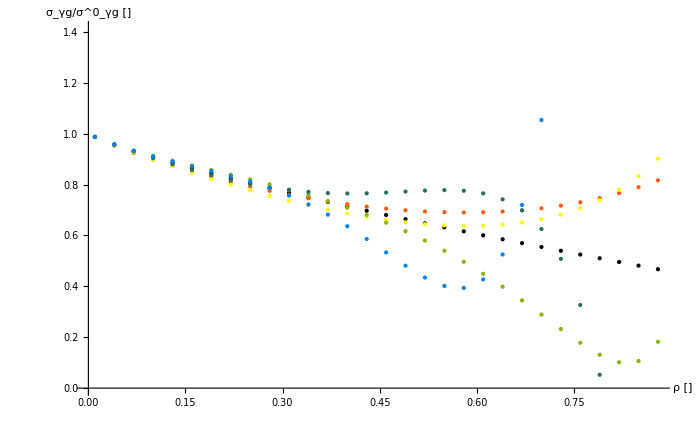

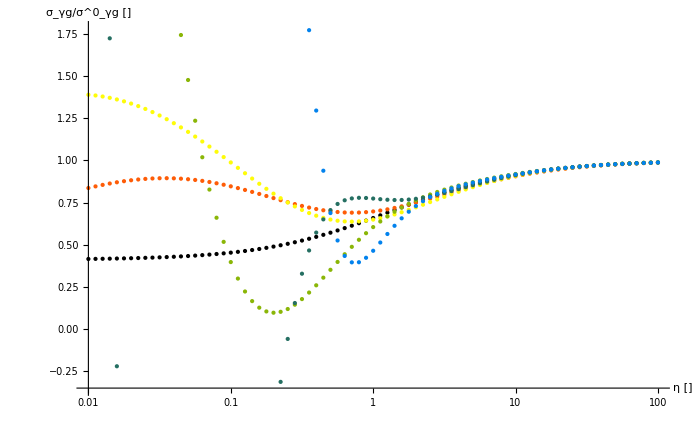

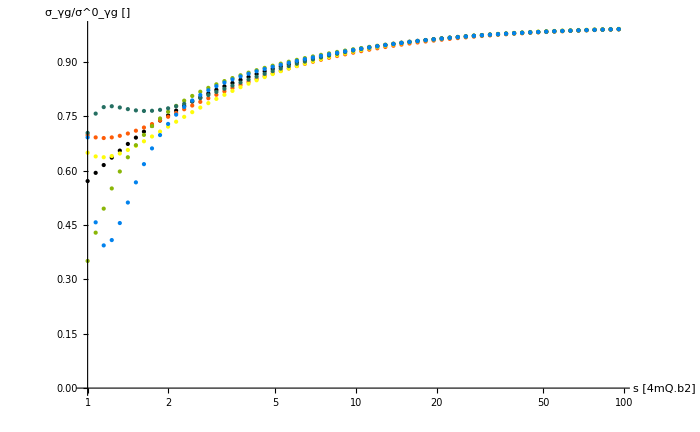

```mathematica
(*
 overall picture:
first element refers to full resummation
plot different variables: ρ,η,s
*)
Module[{v,orders,
fullN,serΔLLMax,serΔLLs,serNs,fullρ,serρs,
computeOnGrid,
ρs,lρs,toρPlot,
ηs,lηs,toηPlot,
ss,lss,tosPlot
},
v=1; (* σ ~ β^v <-> Beta[n,v/2+1] *)
orders={2,3,5,7,10};(* At which orders should the expansion be taken? *)
(* get series *)
serΔLLMax = Normal@Series[ΔLL,{lnN,0,Max@orders}];
serΔLLs =Table[Normal@Series[serΔLLMax,{lnN,0,o}],{o,orders}];
(* build functions *)
fullN = n↦Evaluate[Beta[n,v/2+1]*(ΔLL/.{lnN -> Log[n+1]})];
serNs =(s↦ (n↦Evaluate[Beta[n,v/2+1]*(s/.{lnN -> Log[n+1]})]))/@serΔLLs;
(*Print@fullN;Print@serN;*)
(* compute inverse *)
fullρ = getInvMellinTrafo[fullN//.toN[]];
serρs=(f↦getInvMellinTrafo[f//.toN[]])/@serNs;
(* compute values on grid *)
(* @param xs list to iterate *)
(* @param t transformation function applies to each element in list (to transform to ρ) *)
computeOnGrid[xs_List,t_Function] := Join[
{Parallelize@Table[fullρ[t@x],{x,xs}]},
(fρ↦Parallelize@Table[fρ[t@x],{x,xs}])/@serρs
];
(* equidistant ρ points; equivalent to alter mQ equidistant *)
ρs=Table[j,{j,.01,.9,.03}];
lρs=computeOnGrid[ρs,ρ↦ρ];
toρPlot[l_]:=Transpose[{ρs,l}];
(*Print@lρs;*)
Print@Show[ListPlot[(l↦toρPlot@Re@l)/@lρs,AxesLabel-> {"ρ []","σ_γg/σ^0_γg []"},PlotStyle->ColorData[3,"ColorList"]],ImageSize-> 700];
(* logarithmic η points *)
ηs = Table[10^(j),{j,-2,2,.05}];
lρs=computeOnGrid[ηs,η↦η2ρ@η];
toηPlot[l_]:=Transpose[{ηs,l}];
(*Print@lFullηs;Print@lSerηs;*)
Print@Show[ListLogLinearPlot[(l↦toηPlot@Re@l)/@lρs,AxesLabel-> {"η []","σ_γg/σ^0_γg []"},PlotStyle->ColorData[3,"ColorList"]],ImageSize-> 700];
(* equidistant s points *)
ss = Table[10^j,{j,0,2,.03}];
lss=computeOnGrid[ss,s↦s2ρ[(s*4mQ^2)]//.toN[]];
tosPlot[l_]:=Transpose[{ss,l}];
(*Print@lFullss;Print@lSerss;*)
Print@Show[ListLogLinearPlot[(l↦tosPlot@Re@l)/@lss,AxesLabel-> {"s [4mQ.b2]","σ_γg/σ^0_γg []"},PlotStyle->ColorData[3,"ColorList"]],ImageSize-> 700];
]
```

### Case 1: Threshold limit

First let’s take a look at the threshold region: I conjecture really bad behaviour here, cause any power of ln(N) will introduce a power of ln(β) as I proved in [MSc]

#### Lemma: compare analytic expansion via d_(w,j)(v) to numeric inversion

First let’s check how good the deduced coefficients describe the threshold behavior, so I compare my coefficients d_(w,j)(v) to the numeric inversion of ln^w(N)
Q: Are the coefficients d_(w,j)(v) sufficient near threshold?

```mathematica
(* @param v σ ~ β^v <-> Beta[n,v/2+1] *)
(* @param orders At which orders should the expansion be checked? *)
checkDToNumericInv[v_,orders_List]:=Module[{
ηs,numericFNs,lNumerics,fβs, lAnalytics,lErrs
},
ηs = Table[10^j,{j,-4,0,.03}];
(* compute numeric inversion *)
numericFNs = (o↦(n↦Beta[n,v/2+1]*Log[n+1]^o))/@orders;
lNumerics = (fN↦Parallelize@Table[getInvMellinTrafo[fN][η2ρ@η],{η,ηs}])/@numericFNs;
(* compute analytic inversion *)
fβs=(w↦(β↦β^v*(-1)^w*Sum[getD[w,j,v]*Log[β]^(w-j),{j,0,w}]))/@orders;
(* plot functions *)
(*Print@GraphicsRow[{
ListLogLinearPlot[(l↦Transpose[{ηs,l}])/@lNumerics,PlotStyle->ColorData[3,"ColorList"],AxesLabel-> {"η []","σ_γg/σ^0_γg []"}],
LogLinearPlot[Evaluate[(f↦f[ρ2β@η2ρ@η])/@fβs],{η,Min@ηs,Max@ηs},PlotStyle->ColorData[3,"ColorList"],AxesLabel-> {"η []","σ_γg/σ^0_γg []"}]
},ImageSize->800 ];*)
(* compute analytic at ηs *)
lAnalytics=(f↦Table[f[ρ2β@η2ρ@η],{η,ηs}])/@fβs;
(* compute relative error *)
lErrs = (Re@lNumerics-Re@lAnalytics)/Re@lNumerics;
(* plot errors *)
ListLogLogPlot[(l↦Transpose[{ηs,Abs@l}])/@lErrs,PlotStyle->ColorData[3,"ColorList"],AxesLabel-> {"η []","rel. error []"}]
]
```

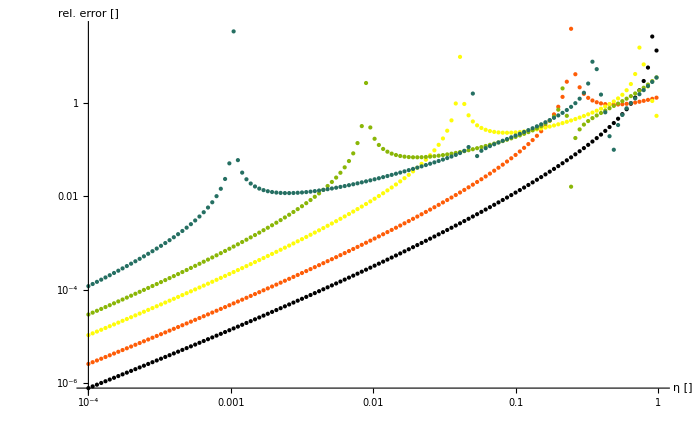

```mathematica
Show[checkDToNumericInv[1,{2,3,5,7,10}] ,ImageSize-> 700]
```

Answer (A): Yes, the coefficients are sufficient;
- the higher the power of ln^w(N), the later is the convergence, but nevertheless they converge
- the peaks to ∞ in the error-plot correspond to zeros of numeric inversion, that doesn’t get matched exactly by analytic inversion
- the peaks to 0 in the error-plot correspond to intersection between, analytic and numeric inversion

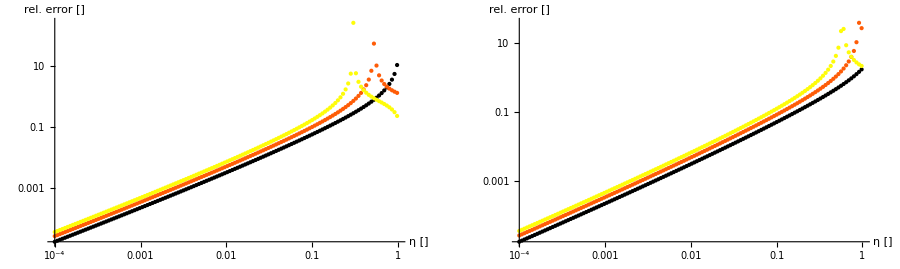

```mathematica
GraphicsRow[{
checkDToNumericInv[3,{2,3,4}],
checkDToNumericInv[5,{2,3,4}]
},ImageSize-> 900]
```

A: this is independent of v;
- propably: the higher v, the faster the convergence

#### Full resummation

The full resummation [is] seems constant > 0 near threshold

```mathematica
(* plot full resummation near threshold *)
(* @param v σ ~ β^v <-> Beta[n,v/2+1]  *)
Options[plotFullAtThreshLimit]={"toN"-> {}};
plotFullAtThreshLimit[v_,opts:OptionsPattern[]]:=Module[{f,ηs,l},
ηs = Table[10^j,{j,-7,0,.1}];
f=n↦Evaluate[Beta[n,v/2+1]*(ΔLL/.{lnN -> Log[n+1]})//.toN[FilterRules[OptionValue["toN"], Options[toN]]]];
l = Parallelize@Table[getInvMellinTrafo[f][η2ρ@η],{η,ηs}];
ListLogLinearPlot[Transpose[{ηs,l}],AxesLabel-> {"η []","σ_γg/σ^0_γg []"}]
];
```

This seems to be independet of v

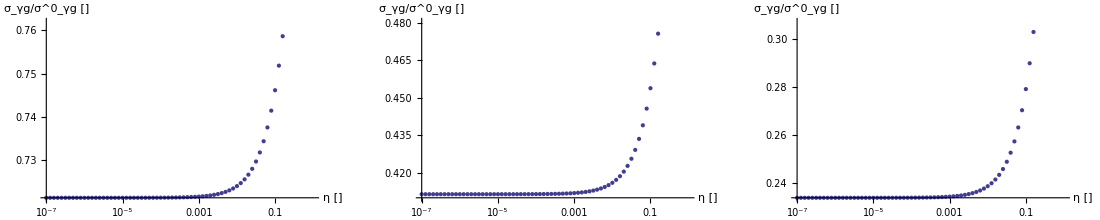

```mathematica
GraphicsRow[{
plotFullAtThreshLimit[0],
plotFullAtThreshLimit[1],
plotFullAtThreshLimit[2]
},ImageSize-> 1100]
```

#### Problems with full resummation

BUT: I would have expected this threshold value to be independent of channel, as N→∞ beats everything, esp. exp(2x) or exp(4x) as the difference between γg and gg8 is;
it isn’t

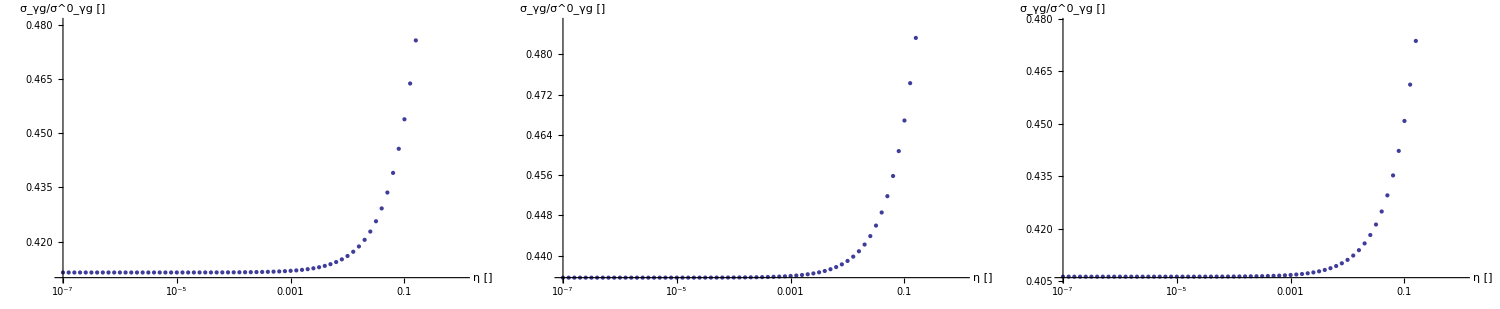

```mathematica
GraphicsRow[{
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "c","channel"-> "γg"}],
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "c","channel"-> "gg8"}],
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "c","channel"-> "qqbar8"}]
},ImageSize->1500,Spacings-> 0]
```

I also expected this threshold value to be independent of quark, as N→∞ beats everything, esp. exp(.36*x) or exp(.15*x) as the difference the quarks/the running coupling,
but it isn’t

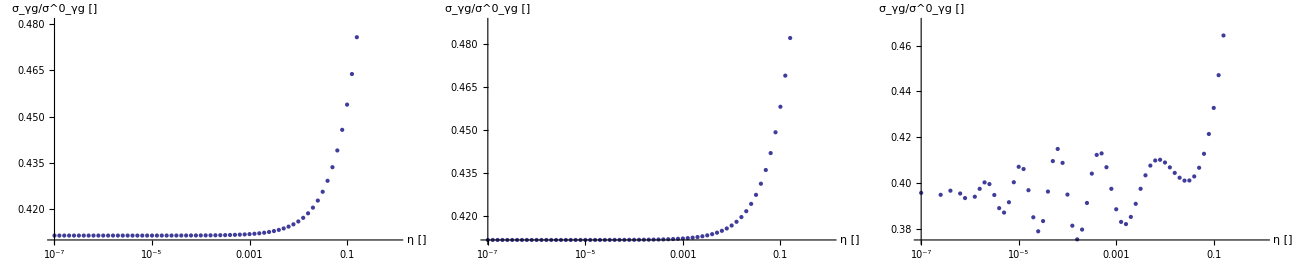

```mathematica
GraphicsRow[{
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "c"}],
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "b"}],
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "t"}]
},ImageSize-> 1300,Spacings-> 0]
```

And, even worse, we seen some wild oscillations occuring before a constant is approached.
This problem rises from α beeing TOO SMALL (!) as can be seen in the following plot:
(NB: mQ→∞ ⇔ αμ→0)

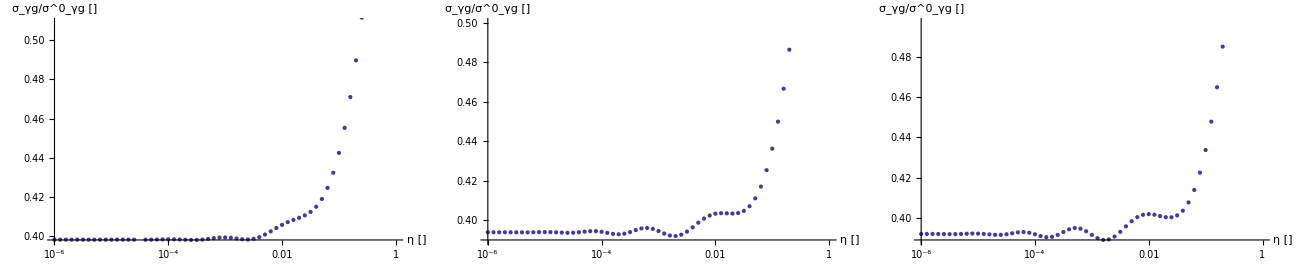

```mathematica
GraphicsRow[{
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "c","mQ"-> 50}],
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "c","mQ"-> 100}],
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "c","mQ"-> 130}]
},ImageSize->1300,Spacings-> 0]
```

of course it also depends on b0, as b0 and α are appearing almost everywhere together: λ=α b0 ln(N) (b0 can be modified by the detected quark b0(charrn) > b0(top))

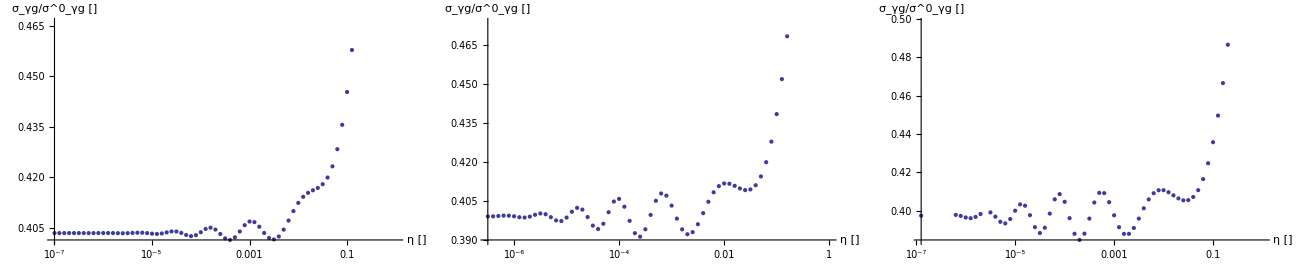

```mathematica
GraphicsRow[{
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "t","mQ"-> 50}],
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "t","mQ"-> 100}],
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "t","mQ"-> 130}]
},ImageSize->1300,Spacings-> 0]
```

Alright lets track this oscillating-problem a bit: it depends strongly on v as can be seen here:

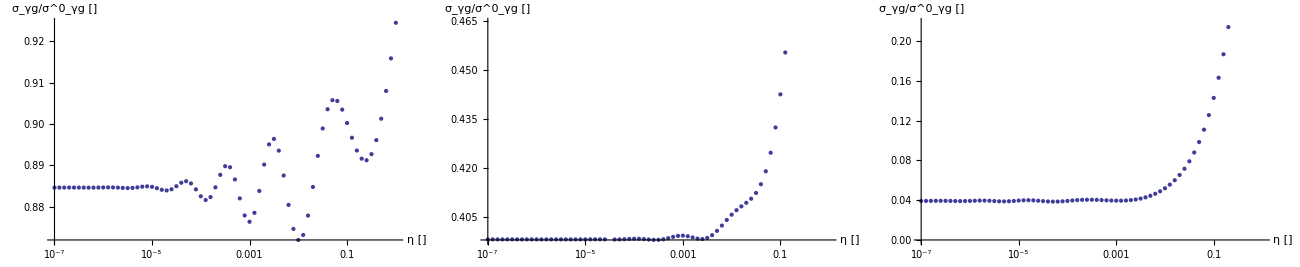

```mathematica
GraphicsRow[{
plotFullAtThreshLimit[0,"toN"-> {"Q"-> "c","αμ"-> .15}],
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "c","αμ"-> .13}],
plotFullAtThreshLimit[2,"toN"-> {"Q"-> "c","αμ"-> .07}]
},ImageSize->1300,Spacings-> 0]
```

It depends on the channel

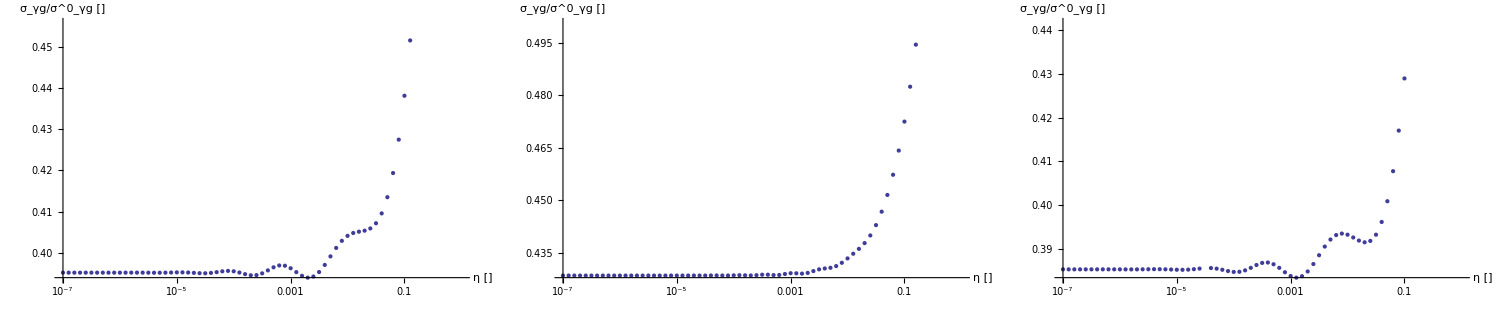

```mathematica
GraphicsRow[{
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "c","channel"-> "γg","αμ"-> .12}],
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "c","channel"-> "gg8","αμ"-> .12}],
plotFullAtThreshLimit[1,"toN"-> {"Q"-> "c","channel"-> "qqbar8","αμ"-> .12}]
},ImageSize->1500,Spacings-> 0]
```

Wild guessing: what form has the exact inversion to take to make such oscillations?

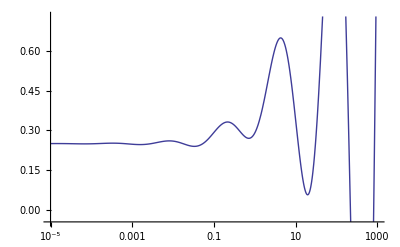

```mathematica
LogLinearPlot[.5-.25η2ρ[η]+.1Sin[2Log@η-1]*Exp[.5Log@η],{η,1*^-5,1*^3}]
```

Alrght:
- I don’t know, why these oscillations are occuring, and why they are appearing for small α
- this oscillation has already be found in [Bonc]
- nevertheless is seems BEYOND these oscillations (i.e. for even smaller η (smaller then in [Bonc])) the function still seems to approach a constant, but this region is numerically instable as well

Let’s see if we can find out a bit more about the threshold value (the constant value I’m suggesting)
Can we specify the dependencies a bit better?

```mathematica
(* plot full resummation for different running couplings αμ or equivalently mQ *)
(* Remember: α,μ ~ 1/ln(mQ) i.e. mQ->0⇒αμ->∞ and mQ->∞⇒αμ->0 *)
(* @param v σ ~ β^v <-> Beta[n,v/2+1]  *)
(* @param ρ ρ-point at which value is calculated  *)
getFullOnRunningPlots[v_,ρ_]:=Module[{f,ms,αμs,lms,lαμs},
f=n↦Beta[n,v/2+1]*(ΔLL//.{lnN -> Log[n+1]});
ms = Table[10^j,{j,0.2,2.5,.1}];
lms = Table[getInvMellinTrafo[n↦Evaluate[f[n]//.toN["mQ"-> m]]][1],{m,ms}];
αμs=Table[j,{j,.15,.8,.03}];
lαμs =Table[getInvMellinTrafo[n↦Evaluate[f[n]//.toN["αμ"-> cαμ]]][ρ],{cαμ,αμs}];
GraphicsRow[{
ListLogLinearPlot[Transpose[{ms,lms}],AxesLabel-> {"m [GeV]","σ_γg/σ^0_γg []"}],
ListPlot[Transpose[{αμs,lαμs}],AxesLabel-> {"αμ []","σ_γg/σ^0_γg []"}]
}]
]
```

We always use real threshold i.e. ρ=1 and we get the following picture:

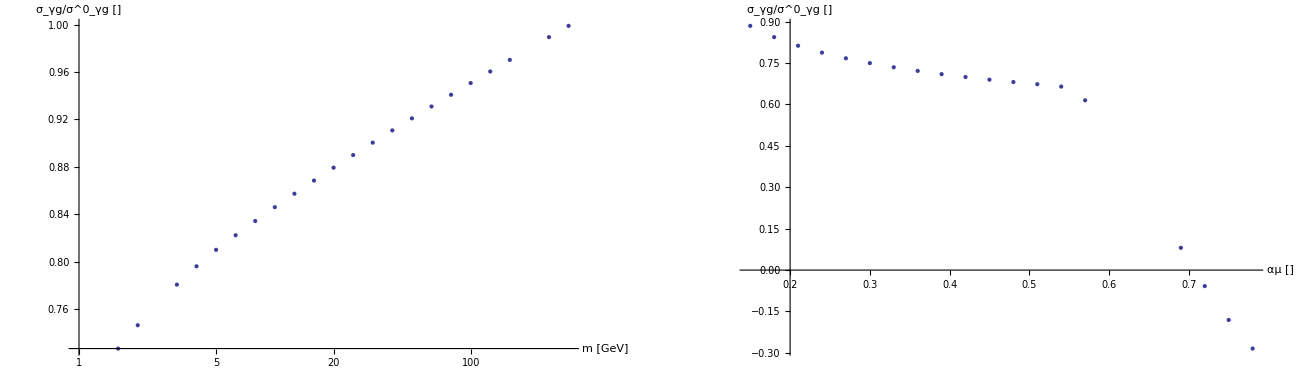

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2158.06  + 1351.24\ ⅈ
 and 1202.38 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 17423.7  + 2537.64\ ⅈ
 and 8183.07 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 76617.3  + 86151.2\ ⅈ
 and 52336.4 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

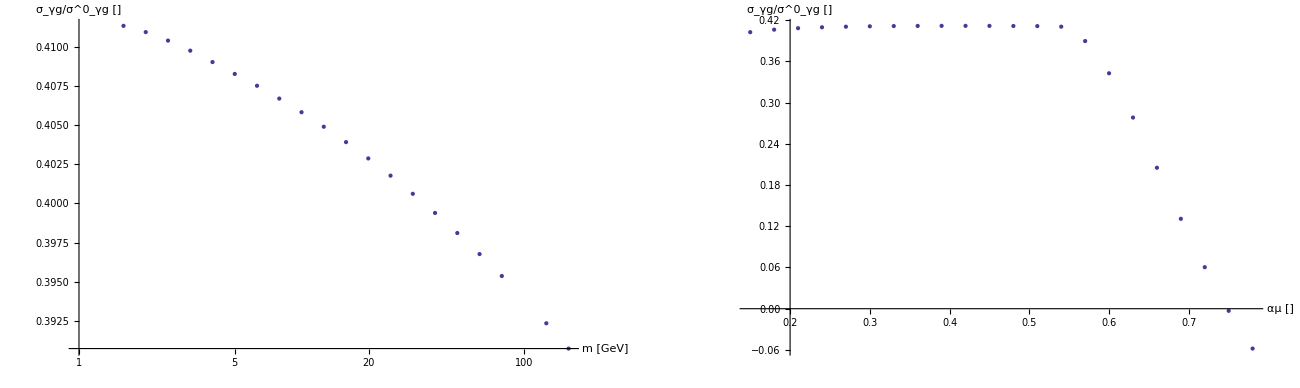

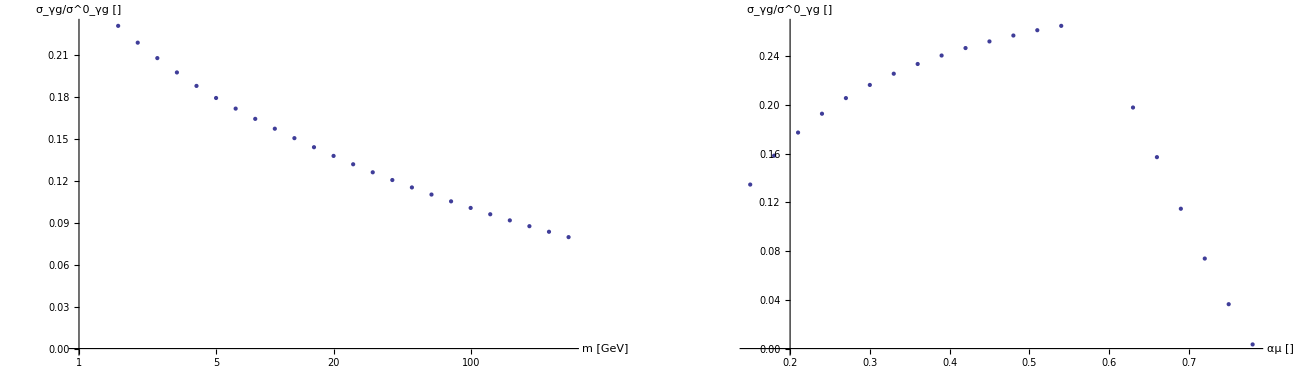

```mathematica
Show[getFullOnRunningPlots[0,1],ImageSize-> 1300]
Show[getFullOnRunningPlots[1,1],ImageSize-> 1300]
Show[getFullOnRunningPlots[2,1],ImageSize-> 1300]
```

And this is even more supprising:
- the shapes for v=1 and v=2 are kind of similar, but v=0 (would correspond to leading Coulomb term) has a different shape
- furthermore we find σ(σ=1) < 0 for αμ getting to large. We would expect problems for αμ getting to large, but does this hold at threshold? I would have expected problems comming to threshold as αμ increases, but at threshold?

#### Reexpansion

The analytic inversion in contrast is f(β→0)→0 as β^v is always stronger then ln(β)^w

```mathematica
Limit[β^v*Log[β],β-> 0,Assumptions-> {v>0}]
```

0

Furthermore the coefficients are wildy oscillating near threshold

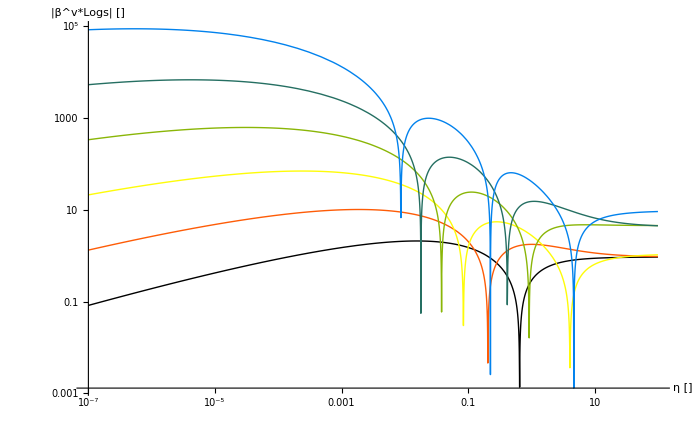

```mathematica
Module[{v,orders,fβs},
v = 1;(* σ ~ β^v <-> Beta[n,v/2+1] *)
orders={2,3,4,5,6,7};
(* compute analytic inversion *)
fβs=(w↦(β↦β^v*(-1)^w*Sum[getD[w,j,v]*Log[β]^(w-j),{j,0,w}]))/@orders;
Show[LogLogPlot[Evaluate[(f↦Abs@f[ρ2β@η2ρ@η])/@fβs],{η,1*^-7,1*^2},PlotStyle->ColorData[3,"ColorList"],AxesLabel-> {"η []","|β^v*Logs| []"}],ImageSize-> 700]
]
```

Problems with the coefficients:
- the higher w, the more real zeros on η in [0,1] exist
- the higher w, the smaller the smallest zero gets
- the higher w, the later is the convergence f(η→0)→0
- the higher w, the higher is e.g. f(η=1e-5)

A: the reexpansion will NOT be related to the full resummation in the threshold limit

#### [probably wrong] don’t use Beta-function in resummation?

- What would be if we just compute the inverse of the raw Sudakov-exponent?
- well, probably this will NOT work, as we need some regularising function - either Beta-function or N^(-k)
- cause “If ϕ(s) is analytic in the strip a < Re(s) < b, and if it tends to zero uniformly as Im(s)→±∞ for any real value c between a and b, with its integral along such a line converging absolutely, then [the inversion exists]”[InvMelTh] and this is clearly not the case as |ln(N)| >= ln(|N|); i.e. the expression grows in all directions
- nevertheless can Mathematica compute the inverse, but this is probably due to the contour-deforming-trick of [MP]; this trick is (I think) numerically needed, but we’re not allowed to be mathematical dependent on it

{1+(lnN^2 αμ ν SudakovFactor`Private`Ak[1])/π,1+(lnN^2 αμ ν SudakovFactor`Private`Ak[1])/π+(2 b0 lnN^3 αμ^2 ν SudakovFactor`Private`Ak[1])/(3 π),1+(lnN^2 αμ ν SudakovFactor`Private`Ak[1])/π+(2 b0 lnN^3 αμ^2 ν SudakovFactor`Private`Ak[1])/(3 π)+(lnN^4 (4 b0^2 π αμ^3 ν SudakovFactor`Private`Ak[1]+3 αμ^2 ν^2 (SudakovFactor`Private`Ak[1])^2))/(6 π^2)}

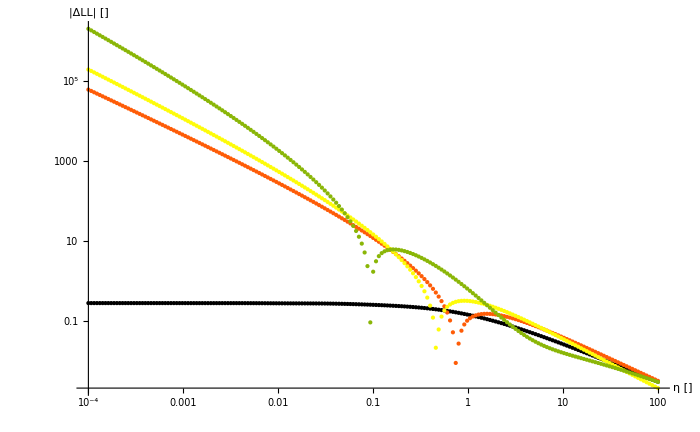

```mathematica
Module[{orders,f,gMaxOrder,gs,gNs,ηs,lf,lNumericgN,analyticgNs,lnN2ρ,ind2w},
orders={2,3,4};
(* build functions *)
f =n↦Evaluate[(ΔLL//.{lnN -> Log[n+1]})//.toN[]];
gMaxOrder=Normal@Series[ΔLL,{lnN,0,Max@orders}];
gs = Table[Normal@Series[gMaxOrder,{lnN,0,w}],{w,orders}];
Print@gs;
gNs=(g↦(n↦Evaluate[g//.{lnN-> Log[n+1]}//.toN[]]))/@gs;
(* plot *)
(*Print[{zPlotReIm[f]}~Join~Table[zPlotReIm@gN,{gN,gNs}]];*)
(* compute on grid *)
ηs=Table[10^j,{j,-4,2,.03}];
lf=Parallelize@Table[getInvMellinTrafo[f][η2ρ@η],{η,ηs}];
lNumericgN  = (gN↦Parallelize@Table[getInvMellinTrafo[gN][η2ρ@η],{η,ηs}])/@gNs;
(*lnN2ρ[w_]=Limit[D[Exp[(k-1)Log@Log[1/ρ]-Log[Gamma[ρ]]],{k,w}],k-> 0];
ind2w[ind_]:=First@ind-1;
analyticgNs=(g↦MapIndexed[Function[{c,ind},c*lnN2ρ[ind2w@ind]],CoefficientList[g,{lnN}]])/@gs;
Print@analyticgNs;*)
(*Print@ListLogLinearPlot[Transpose[{ηs,l}]];*)
Print@Show[ListLogLogPlot[Evaluate[Abs@({Transpose[{ηs,lf}]}~Join~((l↦Transpose[{ηs,l}])/@lNumericgN))],PlotStyle->ColorData[3,"ColorList"],AxesLabel-> {"η []","|ΔLL| []"}],ImageSize-> 700];
(*LogLogPlot[Evaluate[(g↦Abs[g/.{ρ-> η2ρ@η}//.toN[]])/@analyticgNs],{η,1*^-4,1*^2}]*)
]
```

I don’t know how such functions can be inverted ...

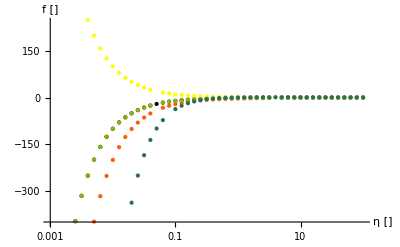

```mathematica
Module[{fNs,ηs,ls},
fNs={n↦1+Log[n],n↦2*Log@n,n↦1-Log[n],n↦Log[n],n↦1+Log[n]^2};
ηs=Table[10^j,{j,-3,2,.1}];
ls=(f↦Parallelize@Table[getInvMellinTrafo[f][η2ρ@η],{η,ηs}])/@fNs;
Print@ListLogLinearPlot[Evaluate[(l↦Transpose[{ηs,l}])/@ls],PlotStyle->ColorData[3,"ColorList"],AxesLabel-> {"η []","f []"}];
]
```

[MP] gave the inversion of ln^w(N)/N^k but this is only valid for Re(k) >0
and yes if we plug k=0 into their formula, we don’t get the same as above

(Log[1/ρ]^(-1+k) Log[Log[1/ρ]]^2)/Gamma[ρ]

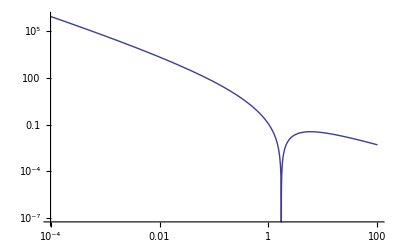

```mathematica
D[Exp[(k-1)Log@Log[1/ρ]-Log[Gamma[ρ]]],{k,2}]
LogLogPlot[Abs[Limit[D[Exp[(k-1)Log@Log[1/ρ]-Log[Gamma[ρ]]],{k,2}],k-> 0]]/.{ρ-> η2ρ@η},{η,1*^-4,1*^2}]
```

as already said is ln^w(N) growing in all directions

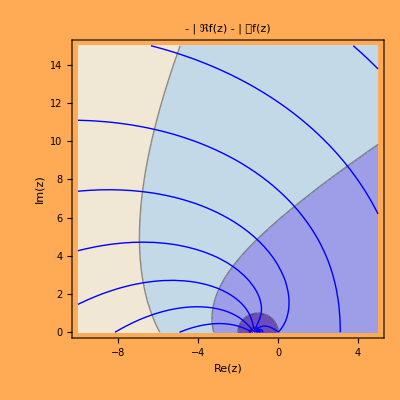

```mathematica
zPlotReIm[n↦Log[n+1]^2,"ymin"-> 0,"xmin"-> -10,"ymax"-> 15]
```

### Case 2: High-energy limit

NB: this section is really theoretical, as I can NOT say, whether resummation is physically valid at all in this limit; so for the moment let’s forget the physics and compare the functions in a mathematical point of view
NB: this limit is numerically unstable[MSc], so I have to guess a bit, and this is why MMa is complainig about “suspect highly oscillatory integrand”; yes, it is
NB: unfortunaly I first forgot the shift to N+1, and it turns out this changed the picture completly - so yes the shift is important (and from this, I think, we can conclude HE-Limit ⇔ ρ→0⇔N→1(0?))

```mathematica
(* @param v σ ~ β^v <-> Beta[n,v/2+1] *)
(* @param orders At which orders should the expansion be checked? *)
getDiffHELimit[v_,orders_]:=Module[{
fullN,serΔLLMax,serΔLLs,serNs,fullρ,serρs,
ss,lFull,lSer,tosPlot
},
(* get series *)
serΔLLMax = Normal@Series[ΔLL,{lnN,0,Max@orders}];
serΔLLs =Table[Normal@Series[serΔLLMax,{lnN,0,o}],{o,orders}];
(* build functions *)
fullN = n↦Evaluate[Beta[n,v/2+1]*(ΔLL/.{lnN -> Log[n+1]})];
serNs =(s↦ (n↦Evaluate[Beta[n,v/2+1]*(s/.{lnN -> Log[n+1]})]))/@serΔLLs;
(* compute inverse *)
fullρ = getInvMellinTrafo[fullN//.toN[]];
serρs=(f↦getInvMellinTrafo[f//.toN[]])/@serNs;
(* compute values on grid *)
ss = Table[10^j,{j,1,3,.03}];
lFull = Parallelize@Table[fullρ[s2ρ[s*4mQ^2]//.toN[]],{s,ss}];
lSer = (fρ↦Parallelize@Table[fρ[s2ρ[s*4mQ^2]//.toN[]],{s,ss}])/@serρs;
(* Plot *)
tosPlot[l_]:=Transpose[{ss,l}];
(*Print@Show[ListPlot[tosPlot@Re@lFull,AxesLabel-> {"s [4mQ.b2]","σ_γg/σ^0_γg []"}],ImageSize-> 700];*)
ListLogLogPlot[(l↦tosPlot@Abs[(Re@l-Re@lFull)/Re@lFull])/@lSer,AxesLabel-> {"s [4mQ.b2]","rel. error []"},PlotStyle->ColorData[3,"ColorList"]]
]
```

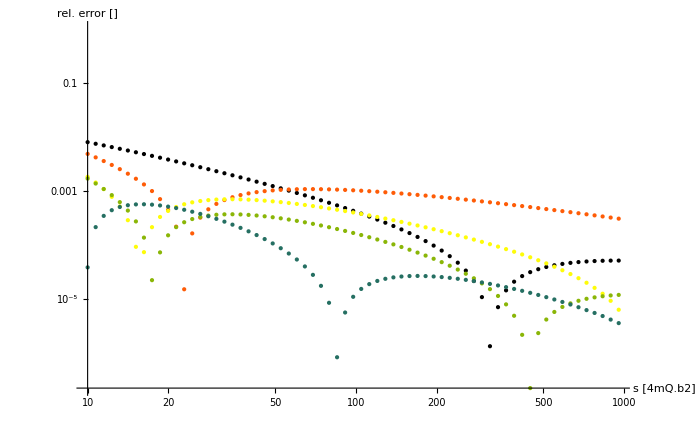

```mathematica
Show[getDiffHELimit[1,{2,3,5,7,10}],ImageSize-> 700]
```

A: Yes, the reexpansion will converge towards the full resummation
- it oscillates around full resummation
- the higher the expansion, the smaller gets the amplitude
- the higher the expansion, the faster gets the frequency

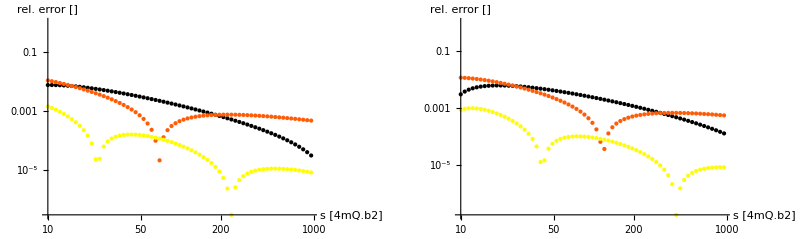

```mathematica
GraphicsRow[{
getDiffHELimit[3,{2,3,10}],
getDiffHELimit[5,{2,3,10}]
},ImageSize-> 800]
```

A: this is independent of v
A: as proved above, the series coefficients of Born cross section sum up to 0, so for full Born resummation the function DOES NOT converge to 1 but to 0 as they are cancelling eachother

```mathematica
(* @param v σ ~ β^v <-> Beta[n,v/2+1] *)
(* @param orders How many orders should be considered for expansion? *)
getDiffStrictHELimit[v_,ks_]:=Module[{
fullN,cutLnΔLL,serΔLLMax,serΔLLs,serNs,fullρ,serρs,
ss,lFull,lSer,tosPlot
},
orders=2*ks;
(* get series *)
cutLnΔLL = Normal@Series[Log[ΔLL],{lnN,0,2}];
serΔLLMax = Normal@Series[Exp@cutLnΔLL,{lnN,0,Max@orders}];
serΔLLs =Table[Normal@Series[serΔLLMax,{lnN,0,o}],{o,orders}];
(* build functions *)
fullN = n↦Evaluate[Beta[n,v/2+1]*(ΔLL/.{lnN -> Log[n+1]})];
serNs =(s↦ (n↦Evaluate[Beta[n,v/2+1]*(s/.{lnN -> Log[n+1]})]))/@serΔLLs;
(* compute inverse *)
fullρ = getInvMellinTrafo[fullN//.toN[]];
serρs=(f↦getInvMellinTrafo[f//.toN[]])/@serNs;
(* compute values on grid *)
ss = Table[10^j,{j,1,3,.03}];
lFull = Parallelize@Table[fullρ[s2ρ[s*4mQ^2]//.toN[]],{s,ss}];
lSer = (fρ↦Parallelize@Table[fρ[s2ρ[s*4mQ^2]//.toN[]],{s,ss}])/@serρs;
(* Plot *)
tosPlot[l_]:=Transpose[{ss,l}];
(*Print@Show[ListPlot[tosPlot@Re@lFull,AxesLabel-> {"s [4mQ.b2]","σ_γg/σ^0_γg []"}],ImageSize-> 700];*)
ListLogLogPlot[(l↦tosPlot@Abs[(Re@l-Re@lFull)/Re@lFull])/@lSer,AxesLabel-> {"s [4mQ.b2]","rel. error []"},PlotStyle->ColorData[3,"ColorList"]]
]
```

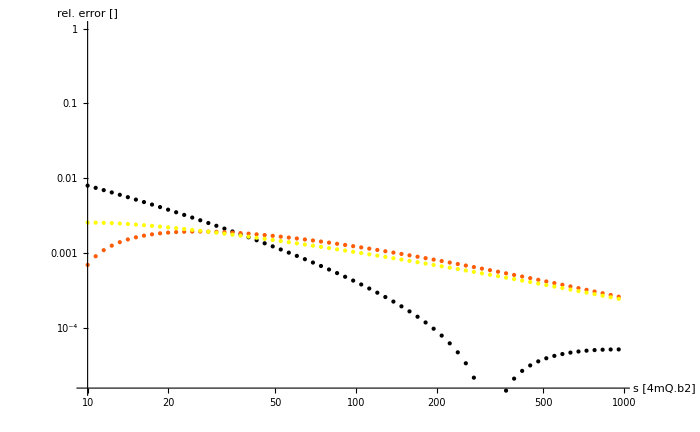

```mathematica
Show[getDiffStrictHELimit[1,{1,2,3}],ImageSize-> 700]
```

A: if one takes, the physically better expansion (NB: I still don’t know, whether this makes sense), i.e. to cut ln(Δ) to ln(N)^2 (as the coefficients below are NOT determined correct) the convergence gets worse, as the full resummation contains these unsatisfied elements

So the overall answer is:
- in the region where we trust resummation, i.e. threshold region, it DOES NOT converge
- and in the region where we don’t trust resummation, i.e. HE region, it DOES converge